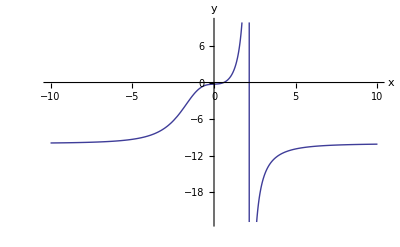

```mathematica
Plot[Tooltip[(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x)),"f(x)= (-30 SuperscriptBox[x, 3] - 3  x + 7 + SuperscriptBox[ⅇ, - .001 x])/(3 SuperscriptBox[x, 3] - 27 - 3 SuperscriptBox[ⅇ, - .001 x])"],{x,-10,10}, AxesLabel->{x,y}]
```

```mathematica
Tooltip[{Graphics[Disk[Dynamic[MousePosition[{"Graphics",Graphics},{0,0}]]],PlotRange->5,ImageSize->250],Graphics[Disk[Dynamic[MousePosition["Graphics",{0,0}]]],PlotRange->5,ImageSize->100]},"Bananas!"]
```

{-Graphics-,-Graphics-}

```mathematica
{Graphics[Disk[],ImageSize->100],Dynamic[MousePosition["Graphics","Mouse not in graphics!"]]}
```

{-Graphics-,}

```mathematica
Dynamic[Plot[f[x],{x,0,10},PlotLabel->Row[{Style["Graph",Italic],PopupMenu[Dynamic[f],{1,2,3,4,5,6}]}],AxesLabel->{x,y}]]
```

```mathematica
Labeled[Framed[{a,b,c,d}],{xxx,yyy},{Left,Top}]
```

{a,b,c,d}xxxyyy

```mathematica
pts = Root[(-30 x^3-3x+7+ⅇ^(-.001x))/(3 x^3-27-3 ⅇ^(-.001x))]
```

Root::trsp: Nonpolynomial root specification 7 + ⅇ^-0.001\ x - 3\ x - 30\ x^3/-27 - 3\ ⅇ^-0.001\ x + 3\ x^3 is not a list with two elements.

Root[(7+ⅇ^(-0.001 x)-3 x-30 x^3)/(-27-3 ⅇ^(-0.001 x)+3 x^3)]

```mathematica
Show[ContourPlot[Abs[(x+I y)^3-27 I],{x,-4,4},{y,-4,4},Contours->15],Graphics[{{Style[Text[#,#],17]&/@#},{Opacity[.5],Orange,Thickness[.01],Arrow[{{0,0},#}]&/@#},{Red,PointSize[.02],Point@#}},Axes->True,Frame->True,PlotRangePadding->1,AspectRatio->Automatic]&@pts]
```

-Graphics-